```mathematica
data = {{6.00,3.081*10^-44},{7.00,7.318*10^-45},{8.00,2.477*10^-45},{9.00,1.072*10^-45},{10.00,5.527*10^-46},{11.00,3.248*10^-46},{12.00,2.108*10^-46},{13.00,1.477*10^-46},{15.00,8.595*10^-47},{17.00,5.866*10^-47},{20.00,4.005*10^-47},{23.00,3.160*10^-47},{25.00,2.838*10^-47},{26.00,2.719*10^-47},{28.14,2.587*10^-47},{30.00,2.616*10^-47},{35.00,2.761*10^-47},{40.00,2.960*10^-47},{45.00,3.188*10^-47},{50.00,3.431*10^-47},{55.00,3.683*10^-47},{60.00,3.939*10^-47},{70.00,4.458*10^-47},{75.00,4.722*10^-47},{80.00,4.988*10^-47},{90.00,5.527*10^-47},{100.00,6.074*10^-47},{125.00,7.468*10^-47},{150.00,8.887*10^-47},{200.00,1.176*10^-46},{500.00,2.857*10^-46},{1000.00,5.636*10^-46},{10000.00,5.636*10^-45}};
```

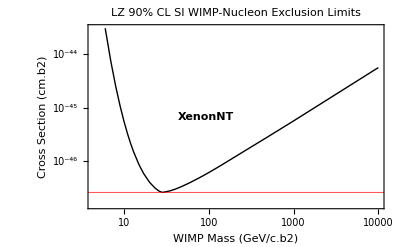

```mathematica
P1=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"WIMP Mass (GeV/c.b2)","Cross Section (cm.b2)"},PlotLabel->"LZ 90% CL SI WIMP-Nucleon Exclusion Limits",  GridLines -> {None, {2.59*10^-47}},  GridLinesStyle -> Directive[Red, Thick],Epilog->{Text[Style["XenonNT",Black,Bold],Scaled[{0.4,0.5}],{-4,3}]}]
```

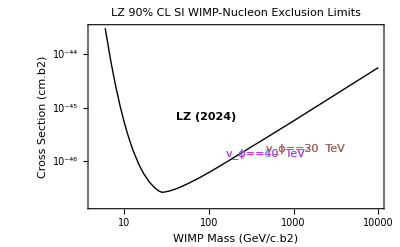

```mathematica
P2=ListLogLogPlot[data,Joined->True,PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"WIMP Mass (GeV/c.b2)","Cross Section (cm.b2)"},PlotLabel->"LZ 90% CL SI WIMP-Nucleon Exclusion Limits",Epilog->{Text[Style["LZ (2024)",Black,Bold],Scaled[{0.4,0.5}],{-4,3}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Cyan],Scaled[{0.6,0.3}],{-9,12}],Text[Style[TraditionalForm[Subscript[v,ϕ]==40 " TeV"],Magenta],Scaled[{0.6,0.3}],{-9,0}],Text[Style[TraditionalForm[Subscript[v,ϕ]==30 " TeV"],Red],Scaled[{0.6,0.3}],{-9,-12.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==20 " TeV"],Gray],Scaled[{0.6,0.3}],{-9,-33}]}]
```

```mathematica
Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Cyan],Scaled[{0.6,0.3}],{-1,5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Magenta],Scaled[{0.6,0.3}],{-3,-2}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-9.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-21}]
```

```mathematica
GeV=5.06 10^13 1/cm
```

(5.06×10^13)/cm

```mathematica
cm=1
```

1

```mathematica
A1=(mDM/(mDM+1))^2g^4/(Pi 9 (g 50 10^3)^4)1/GeV^2/.cm->1;A2=(mDM/(mDM+1))^2 g^4/(Pi 9 (g 40 10^3)^4)1/GeV^2;A3=(mDM/(mDM+1))^2 g^4/(Pi 9 (g 30 10^3)^4)1/GeV^2;A4=(mDM/(mDM+1))^2 g^4/(Pi 9 (g 20 10^3)^4)1/GeV^2;
```

```mathematica
A1/.mDM->10.
```

1.82659×10^-48

```mathematica
A2/.mDM->10
```

4.45945×10^-48

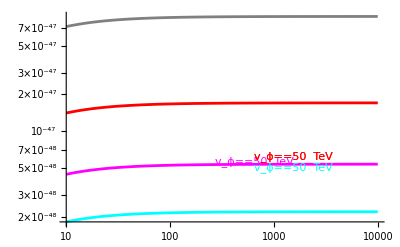

```mathematica
P2=LogLogPlot[{A1,A2,A3,A4},{mDM,10,10^4},PlotStyle->{Cyan,Magenta,Red,Gray},Epilog->{Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Cyan],Scaled[{0.6,0.3}],{-1,7}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Magenta],Scaled[{0.6,0.3}],{-3,-4}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-9.5}],Text[Style[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Red],Scaled[{0.6,0.3}],{-3,-21}]}]
```

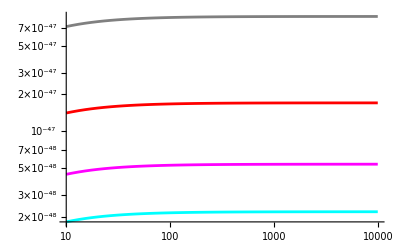

```mathematica
P2=LogLogPlot[{A1,A2,A3,A4},{mDM,10,10^4},PlotStyle->{Cyan,Magenta,Red,Gray}]
```

```mathematica
Text[TraditionalForm[Subscript[v,ϕ]==50 " TeV"],Gray],Scaled[{0.6,0.3}],{-3,-21}
```

```mathematica
A4
```

(8.63349×10^-47 mDM^2)/(1+mDM)^2

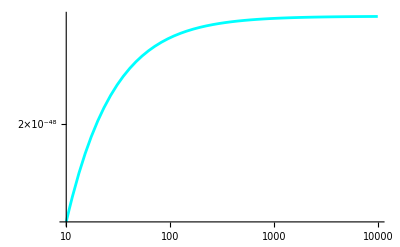

```mathematica
P2
```

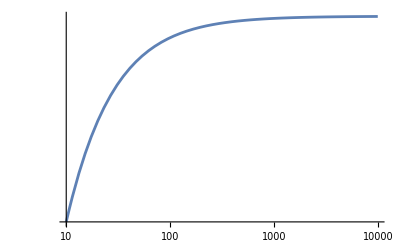

```mathematica
P3=LogLogPlot[A4,{mDM,10,10^4}]
```

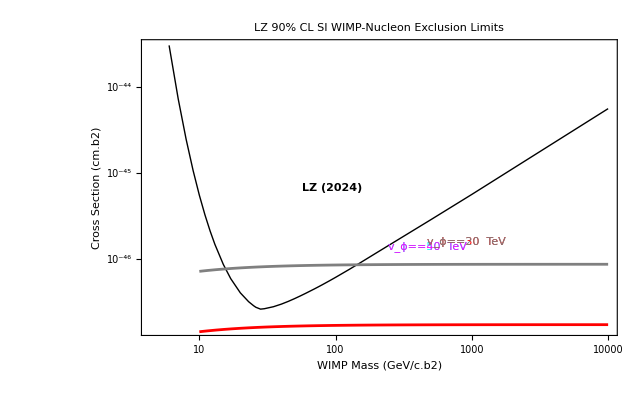

```mathematica
Show[P1,P2]
```